# Brainstorming for Systematic Randomness Testing

```mathematica
Autocorrelation
Recurrence quantification analysis
Recurrence plots
AutocorrelationTest
```

http://www-users.math.umn.edu/~garrett/students/reu/pRNGs.pdf

★

https://en.wikipedia.org/wiki/Kolmogorov% E2 %80 %93 Smirnov_test #Kolmogorov % E2 %80 %93 Smirnov_statistic

https://en.wikipedia.org/wiki/Wald% E2 %80 %93 Wolfowitz_runs _test

https://en.wikipedia.org/wiki/Diehard_tests

https://doc.lagout.org/science/0_Computer %20 Science/2_Algorithms/The%20 Art %20 of %20 Computer %20 Programming %20 %28 vol.%202_ %20 Seminumerical %20 Algorithms %29 %20 %283 rd %20 ed.%29%20 %5 BKnuth %201997-11-14%5 D.pdf

An ultimate report

Bin size vs. p-value

## ✓ Chi Square Test

### Chi Square test for independence — Sequences of 0s and 1s

```mathematica
chiSquareTest01[seq_]:=<|"TestStatistic"->(#2-2#1)^2/#2,"PValue"-> 1.-CDF[ChiSquareDistribution[1],(#2-2#1)^2/#2],"DegreesofFreedom"->1|>&[Total[seq],Length[seq]]
ChiSquareTest[seq_List/;VectorQ[seq,#==0||#==1&]]:=chiSquareTest01[seq]["PValue"];
ChiSquareTest[seq_List/;VectorQ[seq,#==0||#==1&],"PValue"]:=chiSquareTest01[seq]["PValue"];
ChiSquareTest[seq_List/;VectorQ[seq,#==0||#==1&],"TestStatistic"]:=chiSquareTest01[seq]["TestStatistic"];
```

### Chi square test for independence — Random reals between 0 and 1

```mathematica
sequence=RandomReal[{0,1},100];
```

```mathematica
N@1-CDF[ChiSquareDistribution[Length[sequence]-2],Total[(BinCounts[sequence,1/Length[sequence]]-1)^2/1]]
```

0.651641

```mathematica
chiSquareTestRandomReal[seq_]:=Module[{stat=Total[(BinCounts[seq,1/Length[seq]]-1)^2]},
<|"TestStatistic"->stat,"PValue"->1.-CDF[ChiSquareDistribution[Length[seq]-2],stat],"DegreesofFreedom"->Length[seq]-2|>
];
ChiSquareTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&NumberQ[#]&]]:=chiSquareTestRandomReal[seq]["PValue"];
ChiSquareTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&NumberQ[#]&],req_String/;MemberQ[{"TestStatistic","PValue"},req]]:=chiSquareTestRandomReal[seq][req];
```

### Chi square test for independence —Arbitrary distribution

```mathematica
variates=RandomVariate[NormalDistribution[],100];
```

```mathematica
chiSquareTestRandomReal[CDF[NormalDistribution[],variates]]
```

<|TestStatistic→94,PValue→0.595568|>

```mathematica
chiSquareTestArbitraryDistribution[seq_,dist_]:=chiSquareTestRandomReal[CDF[dist,seq]]
```

```mathematica
chiSquareTestArbitraryDistribution[RandomVariate[ChiSquareDistribution[100],1000],ChiSquareDistribution[100]]
```

<|TestStatistic→950,PValue→0.859289,DegreesofFreedom→998|>

## ✓ Kolmogorov-Smirnov Test

```mathematica
sequence=RandomReal[{0,1},100];
```

The Kolmogorov-Smirnov Test is already implemented in the Wolfram Language

```mathematica
KolmogorovSmirnovTest[sequence,UniformDistribution[],"PValue"]
```

0.955143

## ✓ Serial Test — first order

Only works for 0s and 1s!

### Brainstorming

```mathematica
sequence=RandomInteger[{0,1},100]
```

{0,0,1,1,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1,1,0,1,1,1,1,1,1,0,1,1,0,1,0,1,1,1,0,1,0,0,1,1,1,1,1,0,0,0,1,0,0,1,1,1,1,1,0,0,1,0,1,1,0,1,0,1,1,1,0,1,1,1,1,1,0,0,0,1,0,1,1,1,1,0,1,0,1,0,1,0,0,1,1,1}

```mathematica
sequence//Row
```

0011001110000001000101001101111110110101110100111110001001111100101101011101111100010111101010100111

```mathematica
Count[sequence,Sequence[0,1]]
```

5

```mathematica
Count[sequence,#/.List->Sequence]&/@Tuples[{0,1},2]
```

{0,5,0,5}

```mathematica
Replace[Tuples[{0,1},2],List->Sequence,2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Tuples[{0,1},2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]
```

{1,3,4,1}

```mathematica
cts
```

DataDistribution[…]

```mathematica
cts=Table[SequenceCount[RandomInteger[{0,1},100],#]&/@Tuples[{0,1},2],100000]
```

{{12,24,25,13},{19,24,29,15},{13,27,28,19},{15,24,27,11},{17,19,22,17},{19,19,22,23},{19,28,18,15},{16,19,27,14},{13,26,21,16},{9,28,27,13},99980,{14,24,28,16},{17,30,27,20},{16,23,22,18},{8,28,22,15},{19,26,27,15},{10,25,27,20},{18,21,25,19},{16,26,29,21},{15,28,26,18},{12,21,24,17}}
 |  |  |  |

```mathematica
$mcts=N@Mean[cts]
```

{16.5541,24.7637,24.7327,16.5385}

```mathematica
ClearAll[statdist]
```

```mathematica
statdist[num_]:=Module[{n=num,cts=Table[SequenceCount[RandomInteger[{0,1},num],#]&/@Tuples[{0,1},2],100000],mcts},
mcts=N@Mean[cts];
Total[(#-mcts)^2/mcts]&/@N@cts
]
```

```mathematica
statdist[10]
```

{0.66598,4.70229,1.70427,1.33555,1.8321,3.37313,0.66598,99986,0.605268,1.79685,2.88841,0.382571,3.34872,1.04893,3.4083}
 |  |  |  |

```mathematica
df[dist_]:=ν/.FindDistributionParameters[dist,ChiSquareDistribution[ν]]
```

```mathematica
df[statdist[10]]
```

2.35238

```mathematica
Table[df[statdist[n]],{n,100,5000,500}]
```

{2.16794,2.18437,2.16289,2.15685,2.17999,2.17457,2.16051,2.16972,2.17108,2.15506}

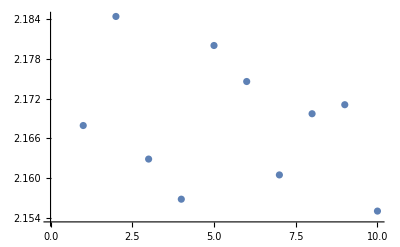

```mathematica
ListPlot[%]
```

```mathematica
ν=df[statdist[1000]]
```

2.18316

★ Test statistic has the form

stat = (freq_(0,0)-n µ_(freq. 0,0))^2/(n µ_(freq. 0,0))+(freq_(0,1)-n µ_(freq. 0,1))^2/(n µ_(freq. 0,1))+(freq_(1,1)-n µ_(freq. 1,1))^2/(n µ_(freq. 1,1))+(freq_(1,0)-n µ_(freq. 1,0))^2/(n µ_(freq. 1,0))
¬stat \[Distributed] χ^2(ν  ≈ 1.90)
stat\[Distributed] GammaDistribution(α,β)

Distribution of test statistic is chi square — for high lengths of (n ≥ 100) sequences ★ CONSTANT ν ★

```mathematica
mcts
```

{16.5541,24.7637,24.7327,16.5385}

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]-$mcts
```

{13,25,24,19}

Mean counts ratio does not vary with sequence length above a certain length

```mathematica
mcts[n_]:=Mean[Table[N@SequenceCount[RandomInteger[{0,1},n],#]&/@Tuples[{0,1},2],10000]]
```

```mathematica
Table[mcts[n]/n,{n,100,5000,500}]
```

{{0.16553,0.2474,0.24766,0.1661},{0.16612,0.249135,0.24996,0.166392},{0.166419,0.249994,0.249593,0.166629},{0.166518,0.249887,0.249653,0.166768},{0.16661,0.249879,0.24989,0.166915},{0.166819,0.249865,0.249909,0.166517},{0.166449,0.249847,0.249868,0.166547},{0.166895,0.250046,0.250115,0.166822},{0.16656,0.249657,0.250096,0.166809},{0.166622,0.250003,0.24997,0.166721}}

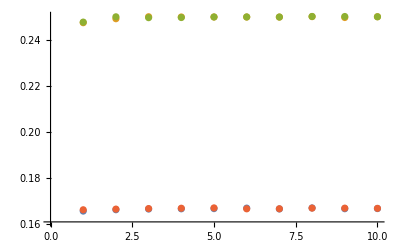

```mathematica
ListPlot[%ᵀ]
```

```mathematica
$mctsrat=mcts[1000]/1000
```

{0.166585,0.249666,0.249679,0.166447}

```mathematica
seqStat[seq_]:=Total[((SequenceCount[seq,#]&/@Tuples[{0,1},2])-Length[seq]$mctsrat)^2/(Length[seq]$mctsrat)]
```

```mathematica
seqStat/@RandomInteger[{0,1},{10^5,1000}];
```

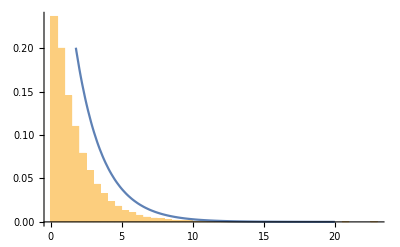

```mathematica
Show[Histogram[%773,Automatic,"Probability",PlotRange->All],Plot[PDF[ChiSquareDistribution[1.9061033494727069],x],{x,0,20}]]
```

```mathematica
FindDistributionParameters[%794,ChiSquareDistribution[n]]
```

{n→1.9061}

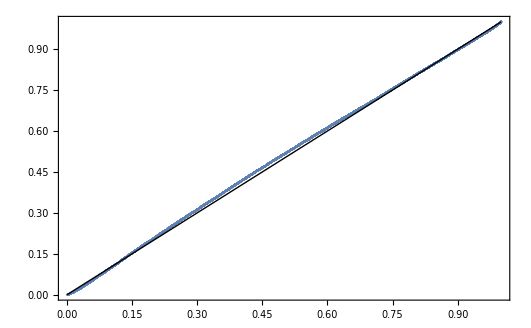

```mathematica
ProbabilityPlot[%794,%812]
```

```mathematica
df[n_]:=degreesOfFreedom/.FindDistributionParameters[seqStat/@RandomInteger[{0,1},{10^5,n}],ChiSquareDistribution[degreesOfFreedom]]
```

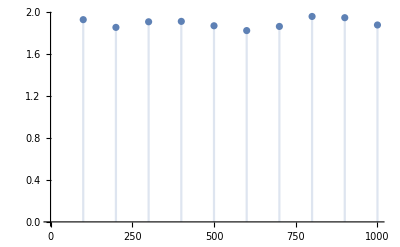

```mathematica
DiscretePlot[df[n],{n,100,1000,100}]
```

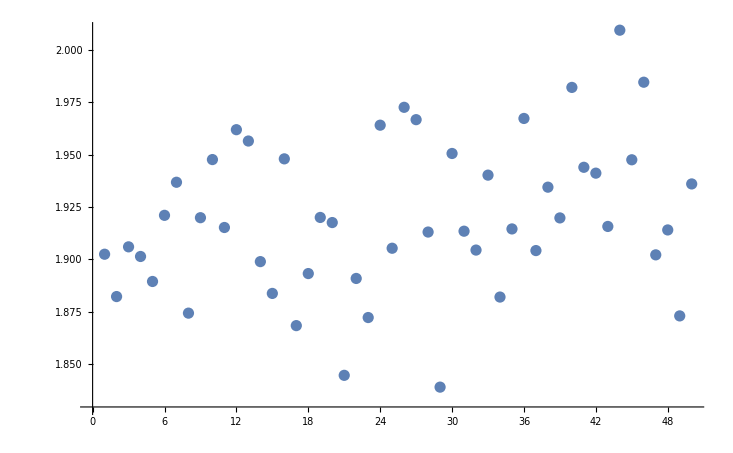

```mathematica
ListPlot[%611]
```

```mathematica
Table[df[n],{n,100,5000,100}];
```

```mathematica
df[1000]
```

1.91098

```mathematica
Tuples[{0,1},2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Table[1-CDF[ChiSquareDistribution[1.91],seqStat[RandomInteger[{0,1},1000]]],10000];
```

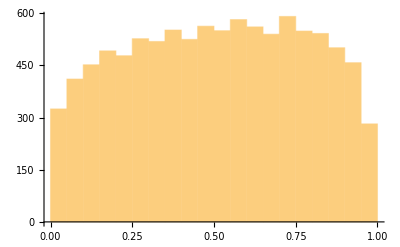

```mathematica
Histogram[%]
```

```mathematica
DistributionFitTest[%750,UniformDistribution[]]
```

0.

Run experiments to show that distribution of stat converges to something else—GammaDistribution?

In paper, note and discuss invariance under list length

```mathematica
FindDistribution[%794,TargetFunctions->{GammaDistribution}]
```

GammaDistribution[1.12244,1.53418]

```mathematica
GammaDistribution
```

```mathematica
Manipulate[Show[Histogram[%794,Automatic,"Probability"],Plot[PDF[%812,x],{x,0,8}]],{ν,0,2}]
```

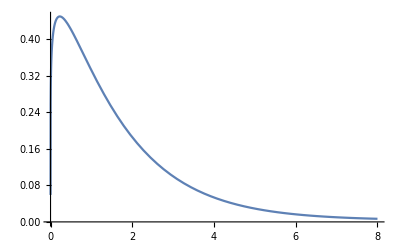

```mathematica
Plot[PDF[%801,x],{x,0,8}]
```

### Procedure & Methods — Outline

Generate a sequence

```mathematica
sequence=RandomInteger[{0,1},100];
sequence//Row
```

1010001010010101011011110011001111011100101110110001100101101011101010011110100011101011001001010010

Format is {{0,0},{0,1},{1,0},{1,1}} for frequency of a sequence.

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]
```

{12,30,31,16}

Find a statistic that measures the deviation from expected frequency

stat = (freq_(0,0)-n µ_(freq. 0,0))^2/(n µ_(freq. 0,0))+(freq_(0,1)-n µ_(freq. 0,1))^2/(n µ_(freq. 0,1))+(freq_(1,1)-n µ_(freq. 1,1))^2/(n µ_(freq. 1,1))+(freq_(1,0)-n µ_(freq. 1,0))^2/(n µ_(freq. 1,0))

Find the mean counts empirically for a given list length n

```mathematica
mcts[n_,samplesize_]:=Mean[Table[N@SequenceCount[RandomInteger[{0,1},n],#]&/@Tuples[{0,1},2],samplesize]]
```

How do these mean counts behave?

```mathematica
ParallelTable[mcts[n,10000]/n,{n,100,1000,100}]
```

{{0.166138,0.247454,0.247369,0.165673},{0.166174,0.248824,0.248729,0.166274},{0.166295,0.248908,0.249039,0.166312},{0.166499,0.249255,0.249211,0.166439},{0.166484,0.249509,0.24975,0.166638},{0.166575,0.249584,0.249569,0.166569},{0.166559,0.249529,0.249706,0.16649},{0.166497,0.249854,0.249716,0.166422},{0.166478,0.249666,0.24974,0.166456},{0.166533,0.249579,0.249745,0.166798}}

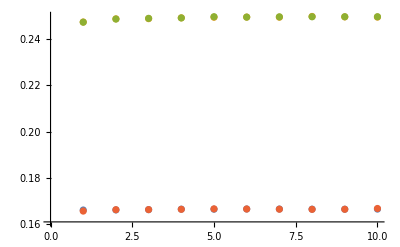

```mathematica
ListPlot[%ᵀ]
```

Ratios between the mean counts and the list length is independent of list length for high (n > 100) list lengths. We can calculate the mean ratios

```mathematica
$mctsrat=mcts[500,100000]/500
```

{0.166482,0.249502,0.249525,0.166416}

Generating the statistic is then easy

```mathematica
seqStat[seq_]:=Total[((SequenceCount[seq,#]&/@Tuples[{0,1},2])-Length[seq]$mctsrat)^2/(Length[seq]$mctsrat)]
```

```mathematica
seqStat[sequence]
```

3.81022

How does this statistic behave?

```mathematica
dist[n_,samplesize_]:=ParallelTable[seqStat[RandomInteger[{0,1},n]],samplesize]
```

```mathematica
distsample500=dist[500,100000];
```

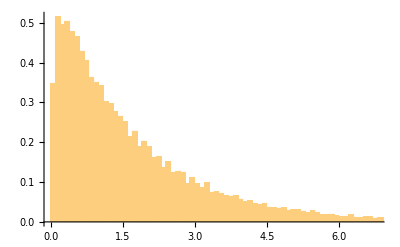

```mathematica
Histogram[distsample500,{.1},"PDF"]
```

This distribution resembles the gamma distribution.

```mathematica
fitdist500=GammaDistribution[α,β]/.FindDistributionParameters[distsample500,GammaDistribution[α,β]]
```

GammaDistribution[1.12973,1.52119]

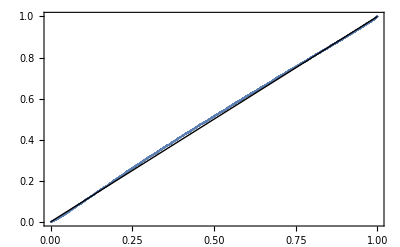

```mathematica
ProbabilityPlot[distsample500,fitdist500]
```

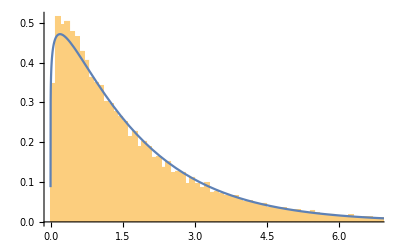

```mathematica
Show[Histogram[distsample500,300,"PDF"],Plot[PDF[fitdist500,x],{x,0,8}]]
```

We can see from the probability plot that this is a very strong fit! We can see that the p-value is low, but not tiny!

```mathematica
DistributionFitTest[distsample500,fitdist500]
```

0.00227318

How do the shape parameters behave with different sequence lengths

```mathematica
αβparams[n_,samplesize_]:=FindDistributionParameters[dist[n,samplesize],GammaDistribution[α,β]]
```

```mathematica
paramvslength=Table[{α,β}/.αβparams[n,10000],{n,100,10000,1000}];
```

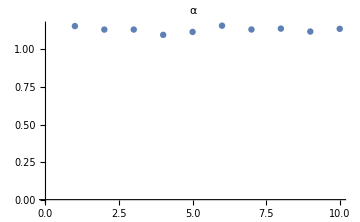
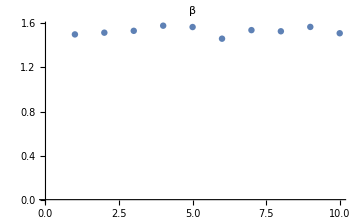

```mathematica
Row@{ListPlot[paramvslengthᵀ⟦1⟧,],ListPlot[paramvslengthᵀ⟦2⟧,]}
```

We can see that the parameters hardly vary and do not vary consistently with list length. We can then find parameters we like.

```mathematica
$params=αβparams[1000,10000]
```

{α→1.11605,β→1.53081}

```mathematica
$fitdist=GammaDistribution[α,β]/.$params
```

GammaDistribution[1.11605,1.53081]

We can now generate p-values

```mathematica
1-CDF[$fitdist,seqStat[sequence]]
```

0.101171

```mathematica
1-CDF[$fitdist,seqStat[#]]&/@RandomInteger[{0,1},{100000,100}];
```

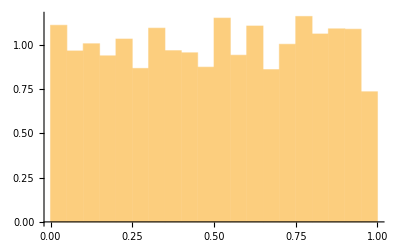

```mathematica
Histogram[%,Automatic,"PDF"]
```

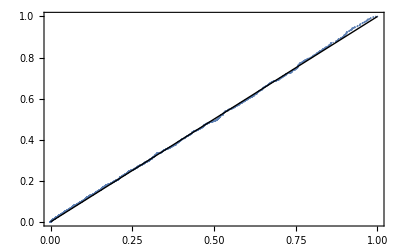

```mathematica
ProbabilityPlot[%977,UniformDistribution[]]
```

We can see that this method is a strong method

## Gap tests

Only on random reals
Page 62 ★

### Brainstorming

```mathematica
sequence=RandomReal[{0,1},1000];
```

```mathematica
Manipulate[BinCounts[Take[sequence,n],.1],{n,1,100,1}]
```

```mathematica
t=9
```

9

```mathematica
r=0
```

0

```mathematica
j=0
```

0

```mathematica
++j;
If[IntervalMemberQ[Interval[{0,.1}],sequence⟦j⟧],,;]
```

32

```mathematica
++j
```

```mathematica
Split[sequence/.x_:>Floor[5 x]+1]
```

{{5},{1,1},{3},{5,5},{2},{1},{4},{1},{4},{3,3},{4},{3},{5},{4},{1},{2},{4},{3,3},{1},{5,5},{2},{1},{2,2},{3},{1},{5,5,5},{2},{3},{2},{4},{5},{4},{2},{1},{2},{3},{5},{4},{3},{4},{3},{1,1},{2,2,2},{1},{2},{4},{1},{4},{3,3},{5},{1,1},{5},{4,4},{3},{4,4},{1},{2},{3},{2},{4},{3,3},{5},{4},{3},{4},{2},{3},{4,4},{2},{1},{2},{4},{5},{2,2,2,2},{4},{3},{4},{1,1,1}}

## Runs test

### Brainstorming

```mathematica
sequence=RandomReal[{0,1},100000];
```

```mathematica
SequenceSplit[sequence/.x_:>Floor[5 x]+1,]
```

SequenceSplit::argtu: SequenceSplit called with 1 argument; 2 or 3 arguments are expected.

SequenceSplit[{5,1,1,3,5,5,2,1,4,1,4,3,3,4,3,5,4,1,2,4,3,3,1,5,5,2,1,2,2,3,1,5,5,5,2,3,2,4,5,4,2,1,2,3,5,4,3,4,3,1,1,2,2,2,1,2,4,1,4,3,3,5,1,1,5,4,4,3,4,4,1,2,3,2,4,3,3,5,4,3,4,2,3,4,4,2,1,2,4,5,2,2,2,2,4,3,4,1,1,1}]

```mathematica
{First[#],Length[#]}&/@Split[sequence/.x_:>Floor[5 x]+1]
```

{{5,1},{1,2},{3,1},{5,2},{2,1},{1,1},{4,1},{1,1},{4,1},{3,2},{4,1},{3,1},{5,1},{4,1},{1,1},{2,1},{4,1},{3,2},{1,1},{5,2},{2,1},{1,1},{2,2},{3,1},{1,1},{5,3},{2,1},{3,1},{2,1},{4,1},{5,1},{4,1},{2,1},{1,1},{2,1},{3,1},{5,1},{4,1},{3,1},{4,1},{3,1},{1,2},{2,3},{1,1},{2,1},{4,1},{1,1},{4,1},{3,2},{5,1},{1,2},{5,1},{4,2},{3,1},{4,2},{1,1},{2,1},{3,1},{2,1},{4,1},{3,2},{5,1},{4,1},{3,1},{4,1},{2,1},{3,1},{4,2},{2,1},{1,1},{2,1},{4,1},{5,1},{2,4},{4,1},{3,1},{4,1},{1,3}}

```mathematica
Subsequences[sequence,{2,1000}]
```

$Aborted[]

p67

```mathematica
runlengths=Length/@Split[RandomReal[{0,1},10000],#1<#2&];
```

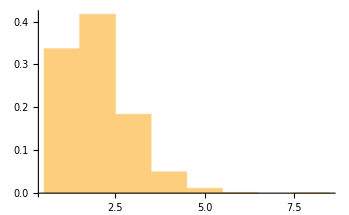

```mathematica
Histogram[%,Automatic,"PDF"]
```

```mathematica
CountsBy[Split[RandomInteger[{0,1},1000]],#⟦1⟧&]
```

<|0→241,1→241|>

```mathematica
runsup[seq_]:=Split[seq,#1<#2&]
```

```mathematica
countRunLength[runsup]
```

<|1→16601,4→2691,2→20833,5→575,3→9118,6→103,7→14,8→3|>

```mathematica
countRunLength[seq_]:=Counts[Length/@Split[seq,#1<#2&]]
```

```mathematica
lengthDist[seq_]:=Length/@Split[seq,#1<#2&]
```

```mathematica
KeyValueMap[#1 #2&,countRunLength[RandomReal[{0,1},1000]]]
```

{384,191,76,306,25,18}

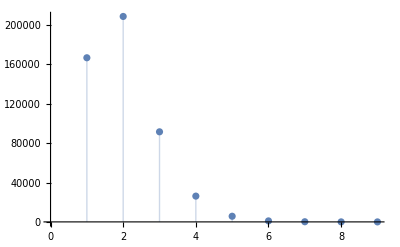

```mathematica
ListPlot[countRunLength[RandomReal[{0,1},1000000]],Filling->Axis]
```

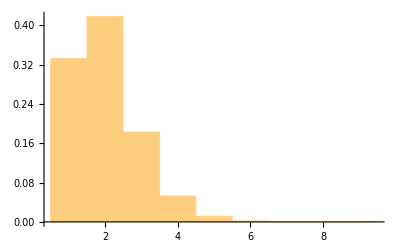

```mathematica
Histogram[lengthDist[RandomReal[{0,1},1000000]],{1},"PDF"]
```

```mathematica
Manipulate[Histogram[lengthDist[Take[sequence,n]],{1},"PDF",PlotRange->{{0,10},{0,1}},PlotLabel->"n = "<>ToString[n]],{n,1,100000,1}]
```

```mathematica
runLenthRatios=Counts[lengthDist[RandomReal[{0,1},1000000]]]/1000000.
```

<|1→0.166616,3→0.091683,4→0.026487,2→0.207977,5→0.005885,6→0.000986,7→0.000135,8→0.000015,9→3.×10^-6|>

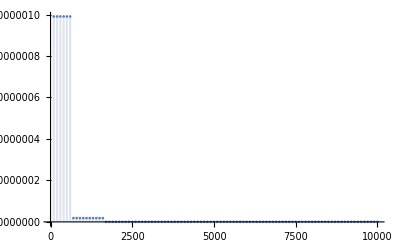

```mathematica
DiscretePlot[Total[Values[KeySort[Append[#1,AssociationThread[Complement[Keys[#1],Keys[#2]]->ConstantArray[0,Length[Complement[Keys[#1],Keys[#2]]]]]]&[runLenthRatios,Counts[lengthDist[Take[#,n]]]/n]-runLenthRatios]]^2],{n,100,10000,100},PlotRange->All]&[RandomReal[{0,1},10000]]
```

Squares difference form 1 million sample distribution length bin counts  vs sample size to constant distribution

```mathematica
meanRunLengths=ParallelMap[ N@Mean[Length/@runsup[#]]&,RandomReal[{0,1},{1000,50000}]];
```

```mathematica
meanRunLengthvsSequenceLength=Table[{n, N@Mean[Length/@runsup[RandomReal[{0,1},n]]]},{n,100,10000,500}]
```

{{100,2.04082},{600,2.04778},{1100,1.99275},{1600,1.99253},{2100,1.9943},{2600,2.0265},{3100,1.97957},{3600,1.99446},{4100,1.95798},{4600,2.00087},{5100,1.98598},{5600,2.01005},{6100,2.00197},{6600,1.99697},{7100,1.99047},{7600,1.99423},{8100,1.99655},{8600,2.01973},{9100,1.9869},{9600,2.01047}}

```mathematica
runLengthDistvsSequenceLength=Table[{n, N@Identity[Length/@runsup[RandomReal[{0,1},n]]]},{n,100,10000,500}]
```

{{100,{1.,1.,2.,1.,1.,2.,1.,1.,2.,3.,1.,1.,1.,1.,2.,1.,1.,2.,5.,2.,2.,1.,3.,2.,2.,2.,1.,3.,1.,4.,4.,3.,2.,2.,1.,4.,2.,1.,3.,1.,1.,1.,3.,1.,2.,1.,2.,3.,5.,1.,3.,1.}},18,{9600,{1.,2.,2.,3.,2.,2.,1.,3.,3.,2.,2.,4.,1.,1.,4729,3.,1.,4.,2.,2.,4.,1.,2.,3.,1.,4.,1.,5.,1.}}}
 |  |  |  |

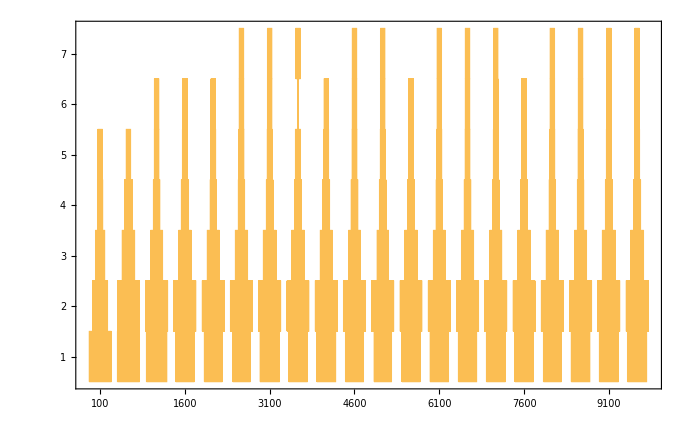

```mathematica
DistributionChart[runLengthDistvsSequenceLengthᵀ⟦2⟧,ChartElementFunction->"HistogramDensity",ChartLabels->runLengthDistvsSequenceLengthᵀ⟦1⟧,PlotRange->{0,All}]
```

Figure above: Runs up lengths vs. sequence length

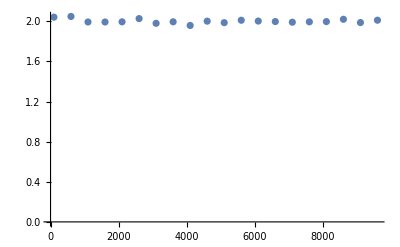

```mathematica
ListPlot[meanRunLengthvsSequenceLength,PlotRange->{0,All}]
```

Figure above: Runs up mean lengths do not vary with sample size

```mathematica
LinearModelFit[meanRunLengthvsSequenceLength,x,x]["RSquared"]
```

0.0644988

```mathematica
$meanRunLengths=N@Mean[Length/@runsup[RandomReal[{0,1},100000]]]
```

1.99406

```mathematica
stat[seq_]:=Total[(seq-$meanRunLengths)^2/($meanRunLengths)]
```

```mathematica
statdist[sequenceLength_,n_]:=stat[#]&/@RandomReal[{0,1},{n,sequenceLength}]
```

```mathematica
Manipulate[ProbabilityPlot[statdist[seqleng,1000]],{seqleng,100,10000,1}]
```

Figure above: The statistic strongly follows a normal distribution

```mathematica
FindDistributionParameters[statdist[]]
```

## ✓ First order differences tests

### Brainstorming – First Order

```mathematica
sequence=RandomReal[{0,1},100000];
```

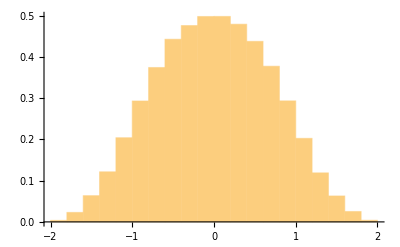

```mathematica
Histogram[Differences[sequence,2],Automatic,"PDF"]
```

```mathematica
TransformedDistribution[X-n,X\[Distributed]UniformSumDistribution[n]]
```

UniformSumDistribution[n,{-1,0}]

```mathematica
TransformedDistribution[X-3,X\[Distributed]UniformSumDistribution[3]]
```

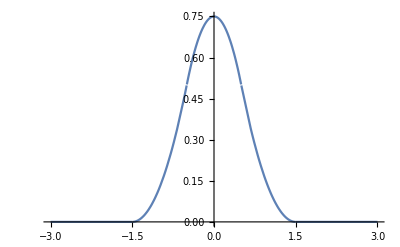

```mathematica
Plot[PDF[TransformedDistribution[X-3/2,X\[Distributed]UniformSumDistribution[3]],x],{x,-3,3}]
```

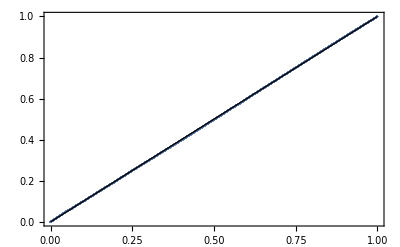

```mathematica
ProbabilityPlot[Differences[sequence,1],TransformedDistribution[X-2/2,X\[Distributed]UniformSumDistribution[2]]]
```

```mathematica
sequence=RandomReal[{0,1},1000];
```

```mathematica
KolmogorovSmirnovTest[Differences[sequence,1],TransformedDistribution[X-1,X\[Distributed]UniformSumDistribution[2]]]
```

0.856546

## Overlapping permutations

### Brainstorm

## Autocorrelation

$Aborted